# Kinematic mount errors for raft on MF03

## PZT 2015.11.09

Nominal ideal ball centers are located at p1={x1,y1}, p2={x2,y2}, and p3={x3,y3}. These are the locations of the vertex angles of the triangle formed by the balls. The kinematic mount is designed so that the lines defined by the vee-groove apex bisect the leg opposite the vertex. With this constraint, all three lines intersect at the centroid point, pc, defined by pc=1/3 (p1+p2+p3), the mean of the three vertex points.

Given the location of each ball center and the common centroid intersection point, it is easy to write an expression for the parametric form of the line through each point and the centroid. Any set of three balls will be constrained to lie on these lines by the kinematic principle. For any set of 3 balls, we can construct the expressions for the distance between each pair of points in terms of the parametric variables. Since we actually measure the distances with the OGP CMM, we can use these values in the distance expressions and solve for the values of the parameters that put the balls on each line segment.

## Start here

#### Start with nominal values for points.

Clear variables

```mathematica
Clear[x1,x2,x3,y1,y2,y3]
Clear[xb1,xb2,xb3,yb1,yb2,yb3]
Clear[d12,d23,d31]
Clear[v1,v2,v3]
```

Define the nominal location of the ideal balls, and the centroid point:

```mathematica
p1={xb1,yb1}={0.,0.};
p2={xb2,yb2}={86.5,0.};
p3={xb3,y3b}={86.5/2,113.5};
```

```mathematica
pc=1/3( p1+p2+p3)(* The centroid point *)
```

{43.25,37.8333}

Set the ideal distances between points:

```mathematica
d12=86.5;
d23=Sqrt[(86.5/2)^2+113.5^2];
d13=Sqrt[(86.5/2)^2+113.5^2];
```

```mathematica
{d12,d23,d13}
```

{86.5,121.461,121.461}

Parametric form of vee-goove lines in terms of vector components. Each line is determined by a vector from the nominal ball center to the centroid point, pc. A point on the line is parametrised by the scalar t.

```mathematica
v1[t1_]:=p1 +(pc-p1) t1; v2[t2_]:=p2 +(pc-p2) t2; v3[t3_]:=p3+(pc-p3)t3;
```

The constraints on the scalar parameter values  are the distances between the balls. 
There are 3 distance constraints: 1->2, 2->3, and 1->3.
Write the distances as functions of points on each relevant line:

```mathematica
dist12=Sqrt[(v2[t2]-v1[t1]).(v2[t2]-v1[t1])]
```

√((86.5-43.25 t1-43.25 t2)^2+(0.-37.8333 t1+37.8333 t2)^2)

```mathematica
dist23=Sqrt[(v3[t3]-v2[t2]).(v3[t3]-v2[t2])];
```

```mathematica
dist13=Sqrt[(v3[t3]-v1[t1]).(v3[t3]-v1[t1])];
```

Now we can measure the actual position of each ball and compute the actual distance. Put these distances in and solve the system of 3 equations for the t-parameters that give the desired separations. Each solution is unique, as there is only one way the kinematic mount can be assembled.
Solve for the values of the parameters that give the desired separation distances.
soln0 is the solution with the balls in the nominal positions. See that the parameter values are 0 for each ball, as they should be.

```mathematica
soln0=FindRoot[{dist12==86.5,dist23==d23,dist13==d23},{{t1,0.1,-0.4,0.4},{t2,0.1,-0.4,0.4},{t3,0.1,-0.4,0.4}}]//Chop
```

{t1→0,t2→0,t3→0}

Check the soln0 result by plugging in the b=0 values into each vee-groove line expression. The {x,y} coords are as they should be.

```mathematica
nomBallCenters={v1[t1],v2[t2],v3[t3]}/.soln0
```

{{0.,0.},{86.5,0.},{43.25,113.5}}

The vector from ball 1 to ball 2 is found by taking the difference between the two points:

```mathematica
vec12=v2[t2]-v1[t1]/.soln0
```

{86.5,0.}

The angle of this vector relative to the global x-axis is given by:

```mathematica
ArcTan[vec12[[2]]/vec12[[1]]]/Degree
```

0.

So the nominal  positions of balls p1 and p2 lie along the global x-axis.

Now plot the kinematic line segments between the balls and the centroid point.  Set the ball radius to a small number so that displacements on the order of microns will be visible in the graphics. You can’t see the balls at the ends of each line segment, but they are there.

```mathematica
ballrad=0.1;
```

```mathematica
nomBalls=Graphics[{Line[{pc,v1[0]}],Line[{pc,v2[0]}],Line[{pc,v3[0]}],
Circle[v1[0],ballrad],Circle[v2[0],ballrad],Circle[v3[0],ballrad]}]
```

-Graphics-

## Now input the actual measured ball centers from MF03 cal data report. The absolute position does not matter, only the relative distances for this analysis. Form the 3 distances with the Norm function.

```mathematica
mb1={0,0};
mb2={86.4893,-0.0158};
mb3={43.3096,113.48888};
```

```mathematica
run$="151113a run3";
mb1={0,0};
mb2={86.4892,-0.01561};
mb3={43.30914,113.48939};
```

```mathematica
run$="151113b run4";
mb1={0,0};
mb2={86.48938,-0.01581};
mb3={43.30966,113.48888};
```

```mathematica
run$="151113c run5";
mb1={0,0};
mb2={86.48922,-0.01622};
mb3={43.31033,113.48899};
```

```mathematica
run$="151113d run6";
mb1={0,0};
mb2={86.48904,-0.01527};
mb3={43.30884,113.48905};
```

```mathematica
run$="151113d run6 reset";
mb1={-0.00043,-0.00107};
mb2={86.48894,-0.0003};
mb3={43.30793,113.48866};
```

```mathematica
run$="151114";
mb1={-0.00073,-0.00031};
mb2={86.48876,-0.00026};
mb3={43.31335,113.4813};
```

```mathematica
run$="151116";
mb1={-0.00059,-0.00042};
mb2={86.49082,0.00028};
mb3={43.31528,113.48569};
```

```mathematica
run$="160122";
mb1={0.0,0.0}(*LL ball*);
mb2={86.4891,-0.0059}(*LR ball*);
mb3={43.3308,113.4747}(*UC ball*);
```

```mathematica
run$="test";
mb1={0.0,0.0}(*LL ball*);
mb2={86.5,0.}(*LR ball*);
mb3={43.25,113.55}(*UC ball*);
```

#### Note: X&Y coords in OGP report are in PCS but have the X&Y labels misidentified. The numbers there need to be switched when entered here.

```mathematica
run$="ECM-004";
mb1={+000.01632,-000.01427}(*LL ball*);
mb2={+086.50150,-000.10007}(*LR ball*);
mb3={+043.23210,-113.53629}(*UC ball*);
```

```mathematica
run$="ECM-005";
mb1={+000.01686,+000.00260}(*LL ball*);
mb2={+086.50142,-000.08126}(*LR ball*);
mb3={+043.23126,-113.51808}(*UC ball*);
```

```mathematica
run$="ECM-005 run4";
mb1={+000.01863,+000.00280}(*LL ball*);
mb2={+086.50528,-000.00367}(*LR ball*);
mb3={+043.35315,-113.47929}(*UC ball*);
```

## Continue from here

```mathematica
{dmb12,dmb23,dmb13}={Norm[mb2-mb1],Norm[mb3-mb2],Norm[mb3-mb1]}
```

{86.4867,121.404,121.475}

Now solve the system for the actual ball center location along the lines that satisfy the distance constraints.

```mathematica
solnmb=FindRoot[{dist12==dmb12,dist23==dmb23,dist13==dmb13},{{t1,0.1,-0.4,0.4},{t2,0.1,-0.4,0.4},{t3,0.1,-0.4,0.4}}]//Chop
```

{t1→-0.000544862,t2→0.000853901,t3→0.000201759}

Put these parameter values into each line equation to get the coords of the ball centers in the system defined by the nominal ball positions.

```mathematica
{mbc1,mbc2,mbc3}={v1[t1],v2[t2],v3[t3]}/.solnmb
```

{{-0.0235653,-0.0206139},{86.4631,0.0323059},{43.25,113.485}}

Compare the actual ball solution positions above to the nominal positions. Compute the displacement of the solution points from the nominal points.

```mathematica
{p1,p2,p3}
```

{{0.,0.},{86.5,0.},{43.25,113.5}}

```mathematica
{mbc1,mbc2,mbc3}-{p1,p2,p3}
```

{{-0.0235653,-0.0206139},{-0.0369312,0.0323059},{0.,-0.0152664}}

Plot the lines from the vee groove centroid to the ball ends.

```mathematica
Graphics[{Line[{pc,v1[0]}],Line[{pc,v2[0]}],Line[{pc,v3[0]}],
Circle[v1[0],ballrad],Circle[v2[0],ballrad],Circle[v3[0],ballrad]},ImageSize->100]
```

-Graphics-

Plot the measured balls in Red

```mathematica
measBalls={Graphics[{Red,Circle[mbc1,ballrad]}],Graphics[{Red,Circle[mbc2,ballrad]}],Graphics[{Red,Circle[mbc3,ballrad]}]};
```

Now overlay both the nominal and actual ball locations. Need to zoom in on each ball location to see the actual displacement of the red from the black.

```mathematica
Show[{nomBalls,measBalls},ImageSize->100]
```

-Graphics-

Need to zoom in on each ball location to see the small displacements:

```mathematica
ballv1=Show[{nomBalls,measBalls},PlotRange->nomBallCenters[[1]]+{{-.2,.2},{-.2,.2}}];
ballv2=Show[{nomBalls,measBalls},PlotRange->nomBallCenters[[2]]+{{-.2,.2},{-.2,.2}}];
ballv3=Show[{nomBalls,measBalls},PlotRange->nomBallCenters[[3]]+{{-.2,.2},{-.2,.2}}];
```

```mathematica
scaleline=Graphics[{Thick,Line[{{0.0,0.0},{0.05,0.0}}],Text[Style["50µm",Large],{0.025,0.10}],Text[Style[run$,Medium],{0.025,-0.10}]}];
showline=Show[scaleline,PlotRange->{0,0}+{{-.2,.2},{-.2,.2}}];
```

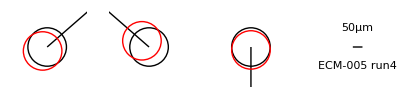

```mathematica
skewballs=GraphicsRow[{ballv1,ballv2,ballv3,showline},ImageSize->400]
```

```mathematica
Export[$HomeDirectory<>"/Desktop/"<>"skewballs.jpg",skewballs]
```

/Users/takacs/Desktop/skewballs.jpg

Note that the actual displaced ball locations are along each respective kinematic vee-groove line. These are the locations of the ideal vee groove centers on the non-ideal balls.

```mathematica
{v1[t1]/.solnmb,v2[t2]/.solnmb,v3[t3]/.solnmb}
```

{{-0.0235653,-0.0206139},{86.4631,0.0323059},{43.25,113.485}}

Now find the angle between the nominal x - axis and the rotated x - axis. Find the vector between the 2 measured points :

```mathematica
vec12m=(v2[t2]-v1[t1])/.solnmb
```

{86.4866,0.0529199}

```mathematica
xaxisangle=ArcTan[vec12m[[2]]/vec12m[[1]]]/Degree
```

0.0350584

This is the effective rotation of non-ideal balls on the ideal kinematic lines. But we actually have the opposite situation: we have an ideal raft sitting on non-ideal balls, where the datum axis is defined by the non-ideal ball positions. So after we measure the actual ball positions and construct the datum origin at the LL ball center with the x-axis through the LR ball, we need to translate and rotate the datum origin and axis direction to line up with the ideal raft datums. So the axis origin gets translated by the negative of the measured ball location on v1:  -mbc1

```mathematica
-mbc1
```

{0.0235653,0.0206139}

And the rotation of the datum x-axis needs to be -xaxisangle:

```mathematica
-xaxisangle
```

-0.0350584

After the datums are redefined about the ball p1, we can further move the datum line to be at the edge of the raft to conform to the raft design drawing offset distance.

```mathematica
run$
```

ECM-005 run4

```mathematica
Print["Run ID: "<>run$<>"\nInput measured ball locations:\n"<>"LL ball: "<>ToString[mb1]<>"\nLR ball: "<>ToString[mb2]<>"\nUC ball: "<>ToString[mb3]<>"\nDistances:"<>"\nLL to LR: "<>ToString[dmb12]<>"\nLL to UC: "<>ToString[dmb13]<>"\nLR to UC: "<>ToString[dmb23]<>"\nOrigin offset and x-axis offset: "<>ToString[{-mbc1,-xaxisangle}]]
```

Run ID: ECM-005 run4
Input measured ball locations:
LL ball: {0.01863, 0.0028}
LR ball: {86.5053, -0.00367}
UC ball: {43.3532, -113.479}
Distances:
LL to LR: 86.4867
LL to UC: 121.475
LR to UC: 121.404
Origin offset and x-axis offset: {{0.0235653, 0.0206139}, -0.0350584}

```mathematica
126*xaxisangle*Degree
```

0.0635405